```mathematica
m:=1.5
d:=3
l:=1
Subscript[m, c]:=Sqrt[3]/2
M:=Sqrt[m^2]
H1=(d-1)/2+Sqrt[((d-1)/2)^2-M^2 l^2];
H2=(d-1)/2-Sqrt[((d-1)/2)^2-M^2 l^2];
norm=Gamma[H1]*Gamma[H2]/((4*π)^(d/2)*l^2*Gamma[d/2]);
W[τ_]:=Limit[norm*Hypergeometric2F1[H1,H2,d/2,1/2*(1+Cosh[τ]+I ϵ)],{ϵ->0.0000000001}]
Wpodal[τ_]:=norm*Hypergeometric2F1[H1,H2,d/2,1/2*(1-Cosh[τ])]
Walpha[τ_,α_,β_]:= Cosh[2α]*W[τ]+Sinh[2α]*(Cos[β]*Re[Wpodal[τ]]-Sin[β]*Im[Wpodal[τ]])
α=N[ArcTanh[E^(-π/2 Sqrt[m^2-1])]]
β=0

Δ[τ_]:= Cos[m τ]/(2 π τ)
```

0.174448

0

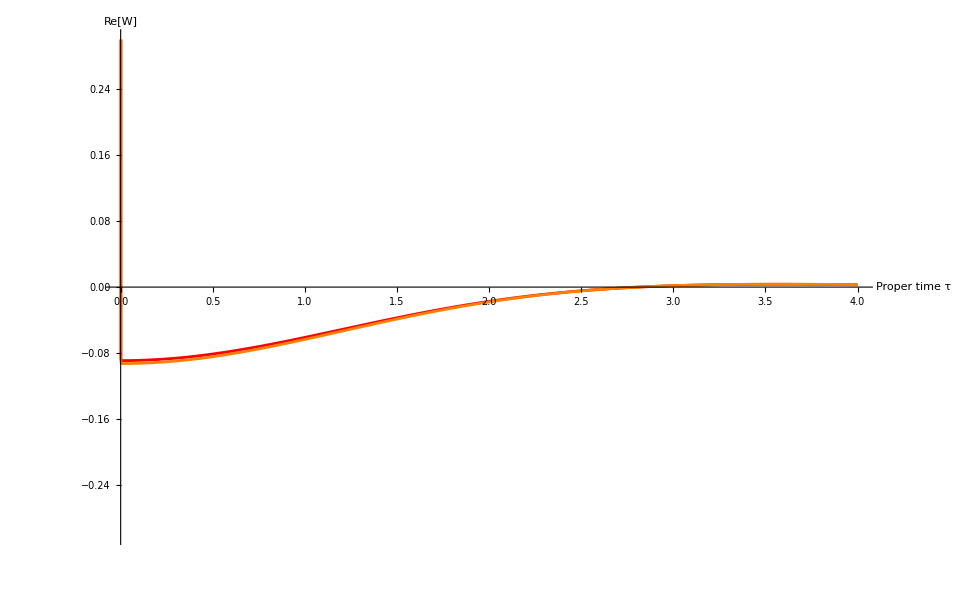

```mathematica
plotLength:=4;
Show[Plot[Re[W[τ]],{τ,0,plotLength},PlotStyle->Red,PlotRange->{{0,plotLength},{-.3,.3}}],
Plot[Re[Walpha[τ,α,β]],{τ,0,plotLength},PlotStyle->Orange,PlotRange->{{0,plotLength},{-.3,.3}}],
AxesOrigin->{0,0},PlotRange->{{0,plotLength},{-.3,.3}},AxesLabel->{"Proper time τ","Re[W]"}]
```

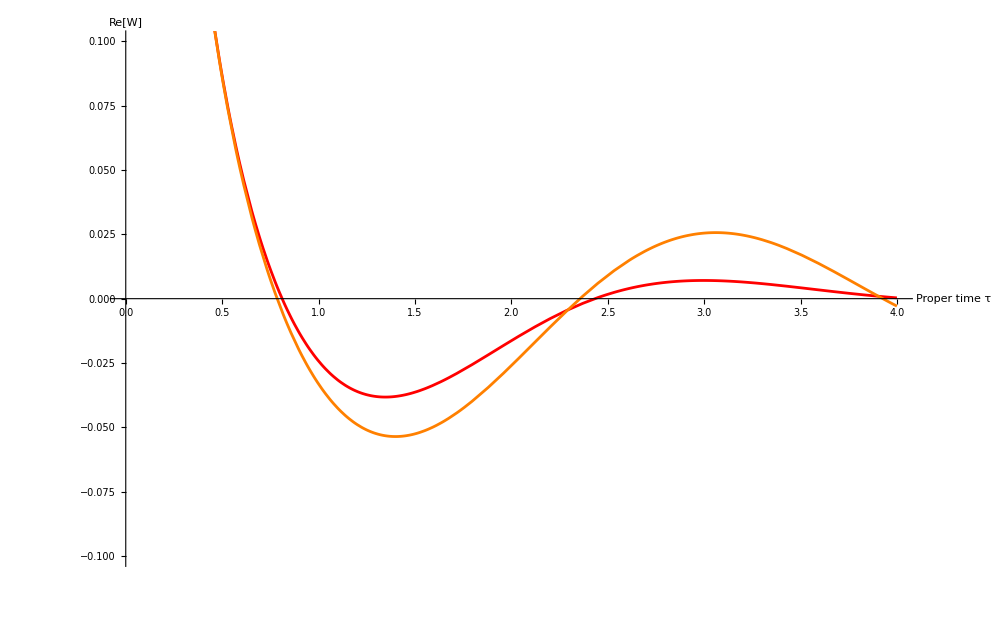

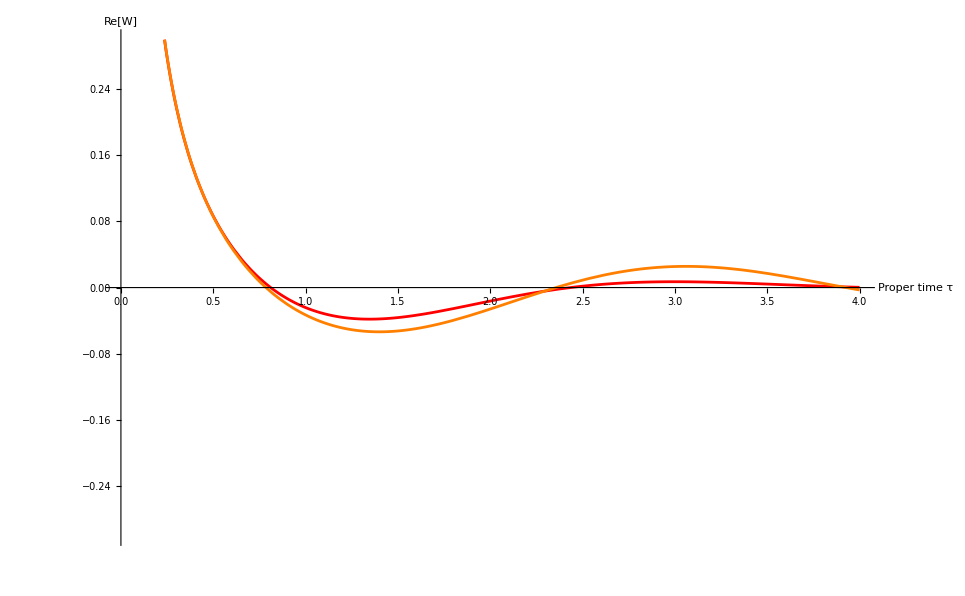

```mathematica
N[Limit[Im[norm*Hypergeometric2F1[H1,H2,d/2,1/2*(1+Cosh[1]+I*ϵ)]],{ϵ->0}]]
Im[Series[2W[τ],{τ,0,4},Assumptions->τ>0]]//FullSimplify
Series[Δ[τ],{τ,0,4}]//FullSimplify
```

Indeterminate

Im[(√3 Csch[(√3 π)/2] Hypergeometric2F1[1-(ⅈ √3)/2,1+(ⅈ √3)/2,3/2,1+ⅈ/2000000])/(4 π)+(7 Csch[(√3 π)/2] Hypergeometric2F1[2-(ⅈ √3)/2,2+(ⅈ √3)/2,5/2,1+ⅈ/2000000] τ^2)/(32 √3 π)+(7 Csch[(√3 π)/2] (20 Hypergeometric2F1[2-(ⅈ √3)/2,2+(ⅈ √3)/2,5/2,1+ⅈ/2000000]+57 Hypergeometric2F1[3-(ⅈ √3)/2,3+(ⅈ √3)/2,7/2,1+ⅈ/2000000]) τ^4)/(7680 √3 π)+O[τ]^5]

1/(2 π τ)-τ/(4 π)+τ^3/(48 π)+O[τ]^5

```mathematica
Limit[Re[N[Limit[norm*Hypergeometric2F1[H1,H2,d/2,1/2*(1+Cosh[ϵ]+I ϵ)],{ϵ->γ}]]],{γ->0}]
```

∞